## Load packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<"ExtFileLoading.wl";
<<"DegFileNamings.wl";
<<"ArrayManip.wl";
<<"PlotMatexFormatting.wl";
SetDirectory[NotebookDirectory[]<>"/.."];
```

## Functions

```mathematica
gWWEcalc[nArr_]:=512/(135 √(3π))nArr^(5/2);
```

```mathematica
gWWEGOEcalc[nArr_]:=π/2 nArr^2;
```

## Read and plot

```mathematica
itNum=100;
seed=1000;
nDim=3;
divLst={80,16,16};
```

```mathematica
nBase=10;
nTop=50;
resBaseLst={16,32};
divLstBaseLst={{80,16,16},{80,32,32}};
resTop=32;
```

```mathematica
nLst=Table[n,{n,10,60,5}];
```

```mathematica
numRes=Length[resBaseLst]+Length[divLstBaseLst];
nMinMaxLst={{10,60},{10,60},{10,85},{10,60}};
nStepLst={5,5,5,5};
nLstLst=Table[Table[n,{n,nMinMaxLst⟦iRes,1⟧,nMinMaxLst⟦iRes,2⟧,nStepLst⟦iRes⟧}],{iRes,1,numRes}];
divLstLst=Table[ConstantArray[divLst,Length[nLstLst⟦iRes⟧]],{iRes,1,numRes}];
```

```mathematica
nLstLst⟦3⟧
```

{10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85}

```mathematica
For[iRes=1,iRes<=Length[resBaseLst],iRes++,
resBase=resBaseLst⟦iRes⟧;
resTop=2resBase;
nLst=nLstLst⟦iRes⟧;
For[iN=1,iN<=Length[nLst],iN++,
mSz=nLst⟦iN⟧;
res=resFun[mSz,nBase,nTop,resBase,resTop];
divLstLst⟦iRes,iN⟧=divLstBaseLst⟦iRes⟧;
divLstLst⟦iRes,iN,2⟧=divLstLst⟦iRes,iN,3⟧=res;]]
For[iRes=1,iRes<=Length[divLstBaseLst],iRes++,
nLst=nLstLst⟦iRes+Length[resBaseLst]⟧;
For[iN=1,iN<=Length[nLst],iN++,
mSz=nLst⟦iN⟧;
divLstLst⟦iRes+Length[resBaseLst],iN⟧=Floor[Sqrt[mSz/nBase]divLstBaseLst⟦iRes⟧];
]]
```

```mathematica
divLstLst⟦3,13⟧
```

{211,42,42}

```mathematica
fMain="deg";
fMethodMod="flux";
```

```mathematica
gTotalMeanLst=Table[ConstantArray[0,{Length[nLstLst⟦iRes⟧]}],{iRes,1,numRes}];
gTotalStdLst=Table[ConstantArray[0,{Length[nLstLst⟦iRes⟧]}],{iRes,1,numRes}];
gWWEMeanLstLst=Table[gWWEcalc[nLstLst⟦iRes⟧],{iRes,1,numRes}];
```

```mathematica
divLstLst⟦1,1⟧
```

{80,16,16}

```mathematica
fName
```

deg_dim_3_N_60_param_divide_[195, 78, 78]_instanceNum_100_seed_1000_flux.jld2

```mathematica
Length[nLstLst⟦3⟧]
```

16

```mathematica
nLstLst⟦1⟧
```

{10,15,20,25,30,35,40,45,50,55,60}

```mathematica
nLst
```

{10,15,20,25,30,35,40,45,50,55,60}

```mathematica
fName
```

deg_dim_3_N_60_param_divide_[195, 78, 78]_instanceNum_100_seed_1000_flux.jld2

```mathematica
divLstLst⟦3⟧⟦13⟧
```

{195,78,78}

```mathematica
For[iRes=1,iRes<=numRes,iRes++,
nLst=nLstLst⟦iRes⟧;
For[iN=1,iN<=Length[nLst],iN++,
mSz=nLst⟦iN⟧;
divLst=divLstLst⟦iRes⟧⟦iN⟧;
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,fMethodMod,jld2Type];
NLstPol=readJuliaVarSq[fName,"NLstPol"];
posNLst=NLstPol⟦1⟧;
gTotalLst=Total[posNLst,{2}];
gTotalMeanLst⟦iRes,iN⟧=Mean[gTotalLst];
gTotalStdLst⟦iRes,iN⟧=StandardDeviation[gTotalLst];
]]
```

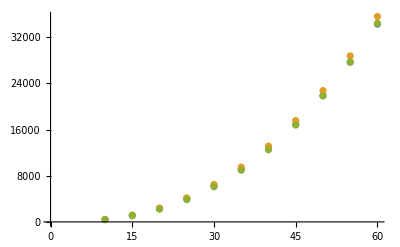

```mathematica
ListPlot[{{nLst,gTotalMeanLst⟦1⟧}ᵀ,{nLst,gTotalMeanLst⟦2⟧}ᵀ,{nLst,gWWEMeanLst}ᵀ}]
```

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"M","\\frac{\\langle N \\rangle}{\\langle N \\rangle_{\\rm WWE}}"};
```

```mathematica
legLst=MaTeX[#,Magnification->labMag]&/@{"20480 M^{0.86}","81920 M^{0.86}","20480 M^{3/2}","81920 M^{3/2}"};
```

```mathematica
legLstStr1={"20480 M^{0.86}","81920 M^{0.86}","20480 M^{3/2}","81920 M^{3/2}"};
legLstStr=Table[legLstStr1⟦id⟧<>","<>ToString[NumberForm[modLst⟦id⟧["ParameterTableEntries"]⟦1,1⟧,{4,3}]]<>"\\pm"<>ToString[NumberForm[modLst⟦id⟧["ParameterTableEntries"]⟦1,2⟧,{4,3}]],{id,1,numRes}];
```

Part::partd: Part specification modLst⟦1⟧ is longer than depth of object.

Part::partd: Part specification modLst⟦1⟧[ParameterTableEntries]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification modLst⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
legLstStr
```

{20480 M^{0.86},0.984\pm0.003,81920 M^{0.86},1.012\pm0.006,20480 M^{3/2},0.998\pm0.005,81920 M^{3/2},1.022\pm0.006}

```mathematica
title=MaTeX["\\frac{\\langle N \\rangle}{\\langle N \\rangle_{\rm WWE}} = A \\exp{\\left(-M / M_0 \\right)} + r_0",Magnification->titleMag];
```

```mathematica
title
```

-Graphics-

```mathematica
legLst=MaTeX[#,Magnification->labMag]&/@legLstStr;
```

```mathematica
legLab=MaTeX["(\\mathrm{resolution},r_0)=",Magnification->labMag];
```

```mathematica
legLab
```

-Graphics-

```mathematica
Log[4]/Log[5]//N
```

0.861353

```mathematica
wweRatLst=Table[{nLstLst⟦iRes⟧,gTotalMeanLst⟦iRes⟧/gWWEMeanLstLst⟦iRes⟧}ᵀ,{iRes,1,numRes}];
```

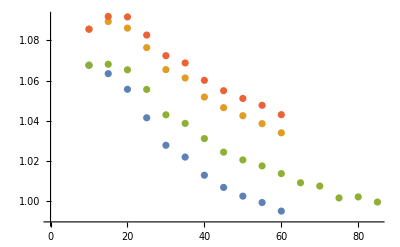

```mathematica
ListPlot[wweRatLst]
```

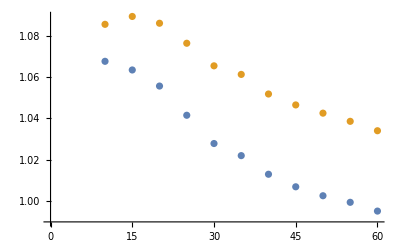

```mathematica
ListPlot[wweRatLst]
```

```mathematica
modLst=Table[NonlinearModelFit[wweRatLst⟦id⟧⟦3;;-1⟧,A Exp[-n/n0]+B,{B,A,n0},{n}],{id,1,numRes}];
```

Part::partd: Part specification wweRatLst⟦1⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

NonlinearModelFit::fitd: First argument Part[] in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification wweRatLst⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

NonlinearModelFit::fitd: First argument Part[] in NonlinearModelFit is not a list or a rectangular array.

Part::partd: Part specification wweRatLst⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Part[] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

```mathematica
modLst⟦2⟧["ParameterTableEntries"]
```

{{1.01215,0.00620946,163.002,3.5966×10^-12},{0.134971,0.00358154,37.6853,2.3306×10^-8},{33.308,4.80367,6.93388,0.000445841}}

```mathematica
modLst
```

{FittedModel[0.983718+0.175749 ⅇ^(-0.0447279 n)],FittedModel[1.01215+0.134971 ⅇ^(-0.0300228 n)],FittedModel[0.988128+0.136329 ⅇ^(-0.0287244 n)],FittedModel[1.02176+0.125158 ⅇ^(-0.0291133 n)]}

```mathematica
modLst⟦1⟧["Function"]
```

0.983718+0.175749 ⅇ^(-0.0447279 #1)&

```mathematica
styleLst⟦1;;10⟧
```

{{GrayLevel[0],AbsoluteThickness[1]},{RGBColor[0.790588, 0.201176, 0.],AbsoluteThickness[1]},{RGBColor[0.192157, 0.388235, 0.807843],AbsoluteThickness[1]},{RGBColor[1., 0.607843, 0.],AbsoluteThickness[1]},{RGBColor[0., 0.596078, 0.109804],AbsoluteThickness[1]},{RGBColor[0.567426, 0.32317, 0.729831],AbsoluteThickness[1]},{RGBColor[0., 0.588235, 0.705882],AbsoluteThickness[1]},{RGBColor[0.8505, 0.4275, 0.13185],AbsoluteThickness[1]},{RGBColor[0.499929, 0.285875, 0.775177],AbsoluteThickness[1]},{RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],AbsoluteThickness[1]}}

```mathematica
Table[modLst⟦id⟧["Function"][n],{id,1,numRes}]
```

{0.983718+0.175749 ⅇ^(-0.0447279 n),1.01215+0.134971 ⅇ^(-0.0300228 n),0.998112+0.139749 ⅇ^(-0.0363402 n),1.02176+0.125158 ⅇ^(-0.0291133 n)}

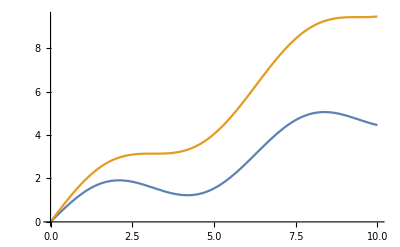

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x},{x,0,10}]
```

```mathematica
funLst=Table[modLst⟦id⟧["Function"][n],{id,1,numRes}]
```

{0.983718+0.175749 ⅇ^(-0.0447279 n),1.01215+0.134971 ⅇ^(-0.0300228 n),0.998112+0.139749 ⅇ^(-0.0363402 n),1.02176+0.125158 ⅇ^(-0.0291133 n)}

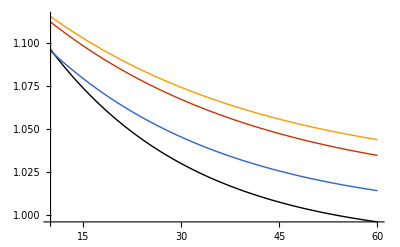

```mathematica
Plot[Evaluate[Table[modLst⟦id⟧["Function"][n],{id,1,numRes}]],{n,10,60},PlotStyle->styleLst]
```

```mathematica
styleLst=Table[{colorLst⟦id⟧,dataThick},{id,1,Length[colorLst]}];
```

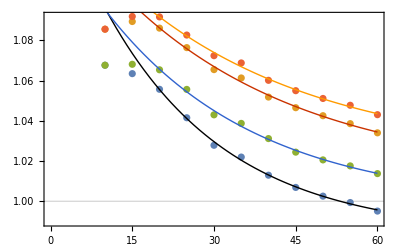

```mathematica
Show[ListPlot[wweRatLst,GridLines->{{},{1}},GridLinesStyle->dataThick,Frame->True,FrameLabel->xyLabs,BaseStyle->texStyle,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotLegends->LineLegend[legLst,LegendLabel->legLab]],
Plot[Evaluate[Table[modLst⟦id⟧["Function"][n],{id,1,numRes}]],{n,10,60},PlotStyle->styleLst],PlotLabel->title]
```

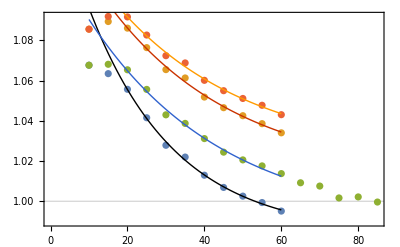

```mathematica
Show[ListPlot[wweRatLst,GridLines->{{},{1}},GridLinesStyle->dataThick,Frame->True,FrameLabel->xyLabs,BaseStyle->texStyle,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotLegends->LineLegend[legLst,LegendLabel->legLab]],
Plot[Evaluate[Table[modLst⟦id⟧["Function"][n],{id,1,numRes}]],{n,10,60},PlotStyle->styleLst],PlotLabel->title]
```

```mathematica
wweRatCell//Dimensions
```

{6,2}

```mathematica
wweRatLst~Join~{wweRatCell}
```

{5}

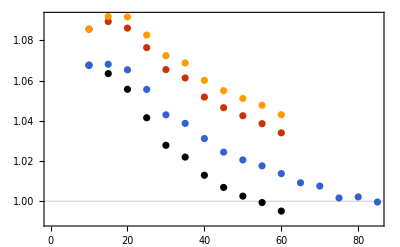

```mathematica
ListPlot[wweRatLst,GridLines->{{},{1}},GridLinesStyle->dataThick,Frame->True,FrameLabel->xyLabs,BaseStyle->texStyle,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotStyle->colorLst,PlotLegends->LineLegend[legLst,LegendLabel->legLab]]
```

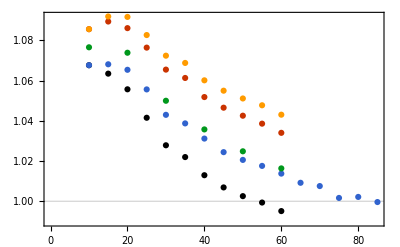

```mathematica
ListPlot[wweRatLst~Join~{wweRatCell},GridLines->{{},{1}},GridLinesStyle->dataThick,Frame->True,FrameLabel->xyLabs,BaseStyle->texStyle,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotStyle->colorLst]
```

```mathematica
legLabCell=MaTeX["\\mathrm{grids\, per\, face}",Magnification->labMag];
legLstCell=MaTeX[#,Magnification->labMag]&/@{"1","16"};
```

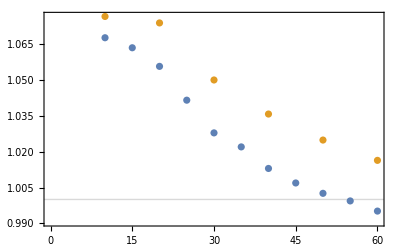

```mathematica
ListPlot[{wweRatLst⟦1⟧,wweRatCell},GridLines->{{},{1}},GridLinesStyle->dataThick,Frame->True,FrameLabel->xyLabs,BaseStyle->texStyle,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotLegends->LineLegend[legLstCell,LegendLabel->legLabCell]]
```

```mathematica
fMethodMod="fluxCell";
nLstLess=Table[n,{n,10,60,10}];
gWWEMeanLstLess=gWWEcalc[nLstLess];
```

```mathematica
gTotalMeanCellLst=ConstantArray[0,{Length[nLstLess]}];
gTotalStdCellLst=ConstantArray[0,{Length[nLstLess]}];
```

```mathematica
For[iN=1;iN2=1,iN<=Length[nLst],iN=iN+2;iN2++,
mSz=nLst⟦iN⟧;
divLst=divLstLst⟦1,iN⟧;
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,fMethodMod,jld2Type];
NLstPol=readJuliaVarSq[fName,"NLstPol"];
posNLst=NLstPol⟦1⟧;
gTotalLst=Total[posNLst,{2}];
gTotalMeanCellLst⟦iN2⟧=Mean[gTotalLst];
gTotalStdCellLst⟦iN2⟧=StandardDeviation[gTotalLst];
]
```

```mathematica
wweRatCell={nLstLess,gTotalMeanCellLst/gWWEMeanLstLess}ᵀ;
```

```mathematica
gTotalMeanCellLst//N
```

{420.58,2373.18,6394.3,12948.1,22381.6,35012.9}

```mathematica
gTotalStdCellLst//N
```

{31.1105,105.936,183.818,264.783,362.434,459.588}

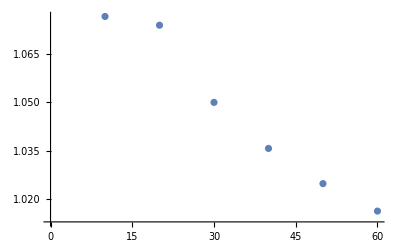

```mathematica
ListPlot[wweRatCell]
```

```mathematica
ListPlot[{nLstLess,gTotalMeanCellLst/gWWEMeanLstLess}ᵀ]
```

-Graphics-

## Same mSz different resolutions

```mathematica
resLst=Table[2^(id-1)16,{id,1,4}];
```

```mathematica
nBase=10;
resBase=16;
```

```mathematica
resLst
```

{16,32,64,128}

```mathematica
divLst
```

{80,36,36}

```mathematica
nLst=Table[n,{n,10,20,10}];
```

```mathematica
gTotalMeanResLst=ConstantArray[0,{Length[nLst],Length[resLst]}];
```

```mathematica
For[iN=1,iN<=Length[nLst],iN++,
mSz=nLst⟦iN⟧;
For[iRes=1,iRes<=Length[resLst],iRes++,
For[iDim=1,iDim<=nDim,iDim++,
divLst⟦iDim⟧=2^(iRes-1)Floor[Sqrt[mSz/nBase]resBase];
];
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,fMethodMod,jld2Type];
NLstPol=readJuliaVarSq[fName,"NLstPol"];
posLst=NLstPol⟦1⟧;
gTotalMeanResLst⟦iN,iRes⟧=Mean[Total[posLst,{2}]];
]]
```

```mathematica
gTotalMeanResLst//N
```

{{403.42,422.38,426.44,427.84},{2262.9,2394.88,2430.72,2437.22}}

```mathematica
gMeanResDat=Table[{resLst,gTotalMeanResLst⟦iN⟧}ᵀ,{iN,1,Length[nLst]}];
```

```mathematica
gRatMeanResDat=Table[{resLst,gTotalMeanResLst⟦iN⟧/gTotalMeanResLst⟦iN,-1⟧}ᵀ,{iN,1,Length[nLst]}];
```

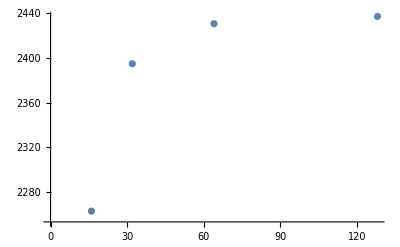

```mathematica
ListPlot[gMeanResDat⟦2⟧]
```

```mathematica
xyLabsRes=MaTeX[#,Magnification->labMag]&/@{"\\left( n_{\\rm cells} \\right)^{1/3}","\\frac{\\langle N \\rangle}{\\langle N \\rangle_{\\rm max}}"};
```

```mathematica
labLstRes=MaTeX["M="<>ToString[#],Magnification->labMag]&/@nLst;
```

```mathematica
labLstRes
```

{-Graphics-,-Graphics-}

```mathematica
xyLabsRes
```

{-Graphics-,-Graphics-}

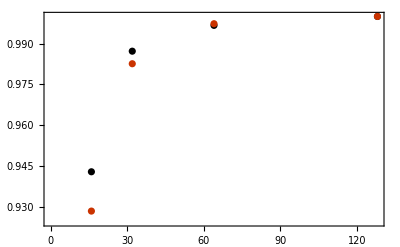

```mathematica
ListPlot[gRatMeanResDat,BaseStyle->texStyle,Frame->True,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotStyle->colorLst,FrameLabel->xyLabsRes,PlotLegends->labLstRes]
```

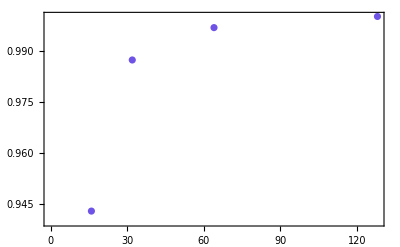

```mathematica
ListPlot[gRatMeanResDat⟦1⟧,BaseStyle->texStyle,Frame->True,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotStyle->colorLst]
```

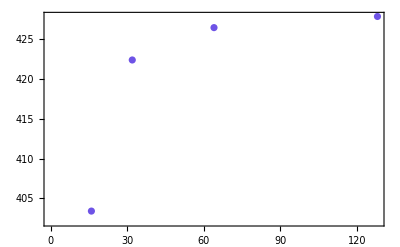

```mathematica
ListPlot[gMeanResDat⟦1⟧,BaseStyle->texStyle,Frame->True,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotStyle->colorLst]
```

```mathematica
ListPlot[gMeanResDat⟦1⟧,BaseStyle->texStyle,Frame->True,ImageSize->{Automatic,6cm},PlotRangePadding->{{None,Automatic},Automatic},PlotStyle->colorLst]
```

## GOE

```mathematica
nDim=2;
nLst=Table[n,{n,10,60,5}];
divLstBase={64,64};
nBase=10;
divLst=divLstBase;
```

```mathematica
gD2MeanLst=ConstantArray[0,Length[nLst]];
```

```mathematica
For[iN=1,iN<=Length[nLst],iN++,
mSz=nLst⟦iN⟧;
divLst=Floor[√(mSz/nBase)divLstBase];
{attrLstDim, valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,fMethodMod,jld2Type];
NLstPol=readJuliaVarSq[fName,"NLstPol"];
posNLst=NLstPol⟦1⟧;
gTotalLst=Total[posNLst,{2}];
gD2MeanLst⟦iN⟧=Mean[gTotalLst];
]
```

```mathematica
gWWELst=gWWEGOEcalc[nLst];
```

```mathematica
fName
```

deg_dim_2_N_60_param_divide_[156, 156]_instanceNum_100_seed_1000_flux.jld2

```mathematica
xyLabsGOE=MaTeX[#,Magnification->labMag]&/@{"M","\\langle N \\rangle"};
```

```mathematica
labLstGOE=MaTeX[#,Magnification->labMag]&/@{"\\mathrm{data}","\\mathrm{WWE}"};
```

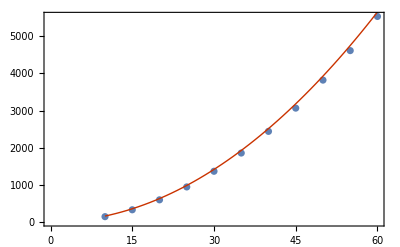

```mathematica
Show[ListPlot[{{nLst,gD2MeanLst/2}ᵀ},PlotLegends->labLstGOE],Plot[gWWEGOEcalc[n],{n,10,60},PlotStyle->{colorLst⟦2⟧,dataThick},PlotLegends->labLstGOE⟦2;;2⟧],BaseStyle->texStyle,Frame->True,ImageSize->{Automatic,6cm},FrameLabel->xyLabsGOE]
```

```mathematica
xyLabsGOERat=MaTeX[#,Magnification->labMag]&/@{"M","\\frac{\\langle N \\rangle}{\\langle N \\rangle_{\\rm WWE}}"};
```

```mathematica
gWilkLst={35,144,564,1370,2489,3847};
nWilkLst={5}~Join~Table[n,{n,10,50,10}];
gWWEWilkLst=gWWEGOEcalc[nWilkLst];
```

```mathematica
nWilkLst
```

{5,10,20,30,40,50}

```mathematica
gD2MeanLst/2//N
```

{141.04,326.34,594.52,941.77,1364.04,1855.06,2438.76,3065.18,3820.06,4614.7,5534.58}

```mathematica
gWWEWilkLst//N
```

{39.2699,157.08,628.319,1413.72,2513.27,3926.99}

```mathematica
gWWEGOEcalc[20]//N
```

628.319

```mathematica
labLstGOERat=MaTeX[#,Magnification->labMag]&/@{"\\mathrm{our \; data}","\\mathrm{WWE\; numerics}"};
```

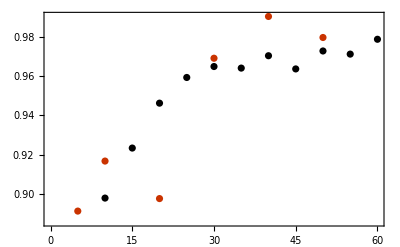

```mathematica
ListPlot[{{nLst,gD2MeanLst/2/gWWELst}ᵀ,{nWilkLst,gWilkLst/gWWEWilkLst}ᵀ},BaseStyle->texStyle,Frame->True,FrameLabel->xyLabsGOERat,ImageSize->{Automatic,6cm},PlotLegends->labLstGOERat,PlotStyle->colorLst]
```

## Misc testing

```mathematica
pkgDir<>"ExtFileLoading.wl"
```

mathematica_nbs/ExtFileLoading.wl

```mathematica
Total[{{1,2,3},{4,5,6}},{2}]
```

{6,15}

```mathematica
texStyle
```

texStyle

```mathematica
texStyle
```

{FontFamily→Times New Roman,FontSize→8,FontWeight→Plain}

```mathematica
FontFamily/.texStyle
```

ReplaceAll::reps: {texStyle} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FontFamily/.texStyle

```mathematica
SetDirectory[NotebookDirectory[]];
<<"PlotMatexFormatting.wl";
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
posNLst//Dimensions
```

{100,60}